```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/baryon_number_fluc

```mathematica
data=Import["./T-mu_500.0-flag_4-150x100_VC=true.csv"];
```

```mathematica
data[[1]]
```

{T_mu,sigma,omega,n_B,P,epsilon}

```mathematica
data[[2]][[1]]
```

(0.0, 500.0)

```mathematica
Head[data[[2]][[1]]]
```

String

```mathematica
StringCases[data[[2]][[1]],NumberString]
```

{0.0,500.0}

```mathematica
T=ToExpression[Table[StringCases[data[[i]][[1]],NumberString][[1]],{i,2,101}]];
mub=ToExpression[Table[StringCases[data[[i*100+2]][[1]],NumberString][[2]],{i,0,149}]];
p=Table[Table[data[[j*100+i]][[5]],{i,2,101}],{j,0,149}];
```

```mathematica
plotdata=Table[Transpose[{T[[2;;100]],(p[[i]][[2;;100]]*197.33^3)/T[[2;;100]]^4}],{i,1,150}];
mubdata=Table[Transpose[{mub,(Transpose[p][[i+1]]*197.33^3)/((*T[[i+1]]^4*)1)}],{i,1,99}];
fitdata=Table[Interpolation[mubdata[[i]],InterpolationOrder->4],{i,1,99}];
chi1=Table[D[fitdata[[i-1]][x],x],{i,2,100}];
chi2=Table[D[fitdata[[i-1]][x],{x,2}][[0]],{i,2,100}];
chi3=Table[D[fitdata[[i-1]][x],{x,3}][[0]],{i,2,100}];
chi4=Table[D[fitdata[[i-1]][x],{x,4}][[0]],{i,2,100}];
```

```mathematica
chi2data=Table[Table[{T[[i+1]],((chi2[[i]][j])/T[[i+1]]^3)},{i,1,99}],{j,500,800,50}];
```

```mathematica
r42data=Table[Table[{T[[i+1]],chi4[[i]][j]/((chi2[[i]][j])/T[[i+1]]^3)},{i,1,99}],{j,500,800,50}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

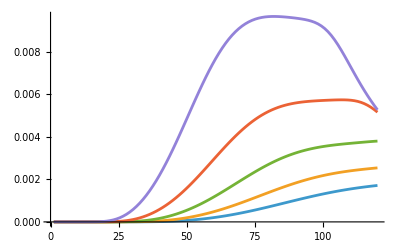

```mathematica
ListLinePlot[chi2data[[1;;5]],PlotRange->{All,All}]
```

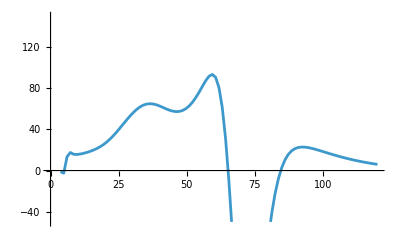

```mathematica
ListLinePlot[r42data[[7]],PlotRange->{All,{-50,150}}]
```

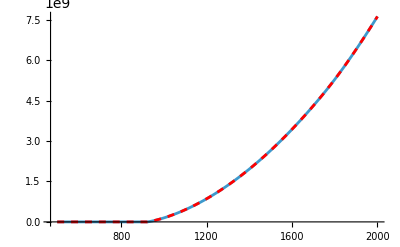

```mathematica
Show[ListLinePlot[mubdata[[1]],PlotRange->All],Plot[fitdata[[1]][x],{x,500,2000},PlotStyle->{Red,Dashed}]]
```